```mathematica
ma=6.015122 ;
mi=170.936323 ;
μ=Sqrt[ma/mi]
```

0.187588

```mathematica
rawcurves=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/3bs/QuickEffV.dat"];
```

```mathematica
Transpose[rawcurves][[2]];
```

```mathematica
U1Dat=Transpose[{Transpose[rawcurves][[1]],Transpose[rawcurves][[2]]}];
```

```mathematica
Dimensions[rawcurves]
```

{8000,11}

```mathematica
U1[x_]:=Interpolation[U1Dat][x]
```

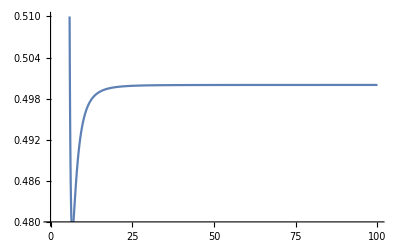

```mathematica
Plot[U1[x],{x,.75,100},PlotRange->{0.48,.51}]
```

For the even states:

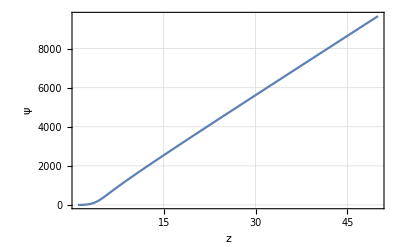

```mathematica
Clear[ψ];ϵ=0.5;ψ=ψ/.NDSolve[{-1/(2 μ)ψ''[z]+U1[z] ψ[z]==ϵ ψ[z],ψ[1]==1,ψ'[1]==0},ψ,{z,0.75,50}][[1]];
Plot[ψ[z],{z,1,50},Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"z","ψ"}]
```

```mathematica
Solve[{A u1==Cos[k x1]-TanDelta Sin[k x1],A u2==Cos[k x2]-TanDelta Sin[k x2]},{A,TanDelta}]//Simplify
```

{{A→Sin[k (x1-x2)]/(u2 Sin[k x1]-u1 Sin[k x2]),TanDelta→(u2 Cos[k x1]-u1 Cos[k x2])/(u2 Sin[k x1]-u1 Sin[k x2])}}

```mathematica
CalcTanDelta[Εtest_,xmax_,xmin_,μ_,V_]:=
Module[{TanDelta,sol,k,u1,u2,x1,x2,u},
x1=0.95 xmax;
x2=0.99xmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[x]+V[x] u[x]==Εtest u[x],u[xmin]==0.001,u'[xmin]==0},u,{x,xmin,xmax}];
u1=u[x1]/.sol[[1]];
u2=u[x2]/.sol[[1]];
TanDelta=(u2 Cos[k x1]-u1 Cos[k x2])/(u2 Sin[k x1]-u1 Sin[k x2]);
Return[TanDelta]
]
```

```mathematica
CalcERE1D[xmin_,xmax_,ΕMin_,ΕMax_,μ_,V_,NumE_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE,ksqr,adata},
dE=(ΕMax-ΕMin)/NumE;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcTanDelta[Εtest,xmax,xmin,μ,V]},{Εtest,ΕMin,ΕMax,dE}];
adata=Table[{Εtest,1/(√(2μ Εtest)CalcTanDelta[Εtest,xmax,xmin,μ,V])},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=1/A/.fitpars;
reff=-2B/.fitpars;
Return[{ascat,reff,EREData,adata}]
]
```

```mathematica
Urel[x]=U1[x]-0.5
```

-0.5+InterpolatingFunction[…][x]

```mathematica
ktandel=CalcERE1D[.75,50.0,0.01,0.9,μ,Urel,100];
```

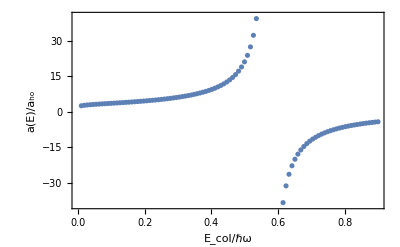

```mathematica
pMathematica1chan=ListPlot[ktandel[[4]],Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"}]
```

```mathematica
CABA1chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/CABAoneChannel.dat"];
CABA1chan=Transpose[Drop[Transpose[CABA1chan],{3}]];
```

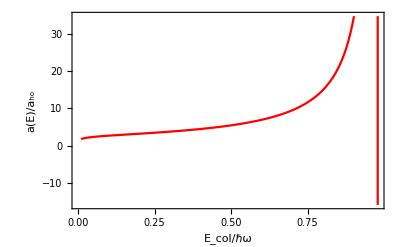

```mathematica
pcaba1chan=ListPlot[CABA1chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Red]
```

```mathematica
CABA6chan=Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/MyCABA/CABA1BS-6chan.dat"];
CABA6chan=Transpose[Drop[Transpose[CABA6chan],{3}]];
```

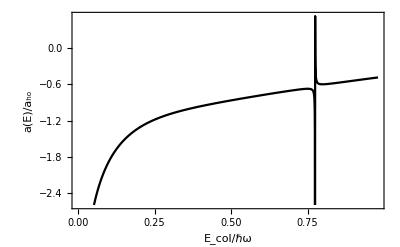

```mathematica
pcaba6chan=ListPlot[CABA6chan,Frame->True,FrameLabel->{"E_col/ℏω","a(E)/a_ho"},Joined->True,PlotStyle->Black]
```

```mathematica
Show[pcaba6chan,pMathematica1chan]
```

-Graphics-

```mathematica
Cos[π-α]
```

-Cos[α]

```mathematica
1/Tan[θc]
```

5.33083

```mathematica
1.07*3400
```

3638.

```mathematica
TrigExpand[Cos[a+b]]
```

Cos[a] Cos[b]-Sin[a] Sin[b]

```mathematica
Cos[π-ϕ]
```

-Cos[ϕ]

```mathematica
Sin[π-ϕ]
```

Sin[ϕ]

```mathematica
3645/3400.
```

1.07206

```mathematica
GegenbauerC[λ,0,x]
```

0

```mathematica
-2!!
```

-2